## Dilepton Case

### Load Parton Level (dσ̂/d Cθ)

```mathematica
SetOptions[{Plot,LogPlot,LogLogPlot,ListPlot,ListLogLogPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,PlotStyle->{Thick},GridLines->Full];
SetOptions[{ListContourPlot},ImageSize->600,AspectRatio->0.7,Frame->True,FrameStyle->15,ContourLabels->True]; (*Plot with frames*)

(* Load dσ/dCθ *)

dσuu2lldCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-uu2ll_X-sec.txt"]];
dσdd2lldCθ=2π ToExpression[Import["/Users/Tae/Desktop/GeoSMEFT/Partonic_cross-section/mW_scheme-dd2ll_X-sec.txt"]];

(*ToParton={s->shat, t->that,u->uhat};*)
```

### Assign Wilson Coefficients

```mathematica
wilsonCoeflist={};
onlySM={};
variablelist = DeleteDuplicates@Cases[dσuu2lldCθ+dσdd2lldCθ,_Symbol,Infinity]
variablelist=Delete[variablelist,{{1},{4}}]

For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[wilsonCoeflist,variablelist[[coef]]->3*10^-5]]
For[coef=1,coef≤ Length[variablelist],coef++,AppendTo[onlySM,variablelist[[coef]]->0.]]


dσuu2lldCθwil = dσuu2lldCθ/.wilsonCoeflist
dσdd2lldCθwil = dσdd2lldCθ/.wilsonCoeflist
dσuu2lldCθSM = dσuu2lldCθ/.onlySM
dσdd2lldCθSM = dσdd2lldCθ/.onlySM
```

{Ein,δGF6,δGF8,Cθ,CLQ36til,CLQ6til,CLu6til,Ceu6til,CeQ6til,CHD6til,CHD28til,CHD8til,CLQs18til,CLQs38til,CLQt18til,CLQt38til,CHec16til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CHuc16til,CeQs8til,CHWB6til,CHB6til,CHW6til,CHWB8til,CeQt8til,CLus8til,CLut8til,CHeQ18til,CHeQ38til,CHLu18til,CHLu38til,CHQ16til,CHQ36til,CHL16til,CHL36til,Ceus8til,Ceut8til,CHeu8til,CHL18til,CHL28til,CHL38til,CHQ18til,CHQ28til,CHQ38til,CHec18til,CHuc18til}

{δGF6,δGF8,CLQ36til,CLQ6til,CLu6til,Ceu6til,CeQ6til,CHD6til,CHD28til,CHD8til,CLQs18til,CLQs38til,CLQt18til,CLQt38til,CHec16til,CHLQ18til,CHLQ28til,CHLQ38til,CHLQ48til,CHuc16til,CeQs8til,CHWB6til,CHB6til,CHW6til,CHWB8til,CeQt8til,CLus8til,CLut8til,CHeQ18til,CHeQ38til,CHLu18til,CHLu38til,CHQ16til,CHQ36til,CHL16til,CHL36til,Ceus8til,Ceut8til,CHeu8til,CHL18til,CHL28til,CHL38til,CHQ18til,CHQ28til,CHQ38til,CHec18til,CHuc18til}

1/(Ein^2 (6.91862×10^7-66521.4 Ein^2+16 Ein^4))2.43925×10^-6 (5.58541×10^8 (1+Cθ^2) (6.91862×10^7-66521.4 Ein^2+16 Ein^4)+0.194901 (-5.04143×10^8 (33259.7 (4.57904-(30003600027 Cθ)/2500000000+4.57904 Cθ^2)+24961.4 (87/100000+(3 (-1+Cθ)^2)/12500+(9 Cθ)/50000+(87 Cθ^2)/100000+(3 (1+Cθ)^2)/12500)) Ein^2+2 (4.03302×10^9 (4.57904-(30003600027 Cθ)/2500000000+4.57904 Cθ^2)+24945.5 (222.222+58.2041 (-1+Cθ)^2+48.895 Cθ+222.722 Cθ^2+3.74421 Cθ^3+58.2041 (1+Cθ)^2)) Ein^4-48 (63.9729+14.551 (-1+Cθ)^2+16.1518 Cθ+64.4719 Cθ^2+3.74183 Cθ^3+14.551 (1+Cθ)^2) Ein^6+96 (99/100000-(21 Cθ)/100000+(81 Cθ^2)/100000+(33 Cθ^3)/100000+(3 (1+Cθ)^2)/12500+(3 (1+Cθ)^3)/25000) Ein^8)+Ein^4 (1.10621×10^9 (8.37443-13.7388 Cθ+8.37443 Cθ^2)+1.64573 (-8315.18+4 Ein^2) (-53.9693+1.23896 (-1+Cθ)^2+130.409 Cθ-53.9693 Cθ^2+0.00166899 Ein^2-0.00380455 Cθ Ein^2+0.000215364 Cθ^2 Ein^2+0.000556331 Cθ^3 Ein^2)+9 (9/400000000+(9 (-1+Cθ)^2)/625000000+(63 Cθ)/5000000000+(9 Cθ^2)/400000000+(9 (1+Cθ)^2)/625000000) (6.91862×10^7-66521.4 Ein^2+16 Ein^4)))

1/(Ein^2 (6.91862×10^7-66521.4 Ein^2+16 Ein^4))2.43925×10^-6 (5.58541×10^8 (1+Cθ^2) (6.91862×10^7-66521.4 Ein^2+16 Ein^4)+0.194901 (-5.04143×10^8 (33259.7 (4.57904-(30003600027 Cθ)/2500000000+4.57904 Cθ^2)+24961.4 (87/100000+(3 (-1+Cθ)^2)/12500+(9 Cθ)/50000+(87 Cθ^2)/100000+(3 (1+Cθ)^2)/12500)) Ein^2+2 (4.03302×10^9 (4.57904-(30003600027 Cθ)/2500000000+4.57904 Cθ^2)+24945.5 (222.222+58.2041 (-1+Cθ)^2+48.895 Cθ+222.722 Cθ^2+3.74421 Cθ^3+58.2041 (1+Cθ)^2)) Ein^4-48 (63.9729+14.551 (-1+Cθ)^2+16.1518 Cθ+64.4719 Cθ^2+3.74183 Cθ^3+14.551 (1+Cθ)^2) Ein^6+96 (99/100000-(21 Cθ)/100000+(81 Cθ^2)/100000+(33 Cθ^3)/100000+(3 (1+Cθ)^2)/12500+(3 (1+Cθ)^3)/25000) Ein^8)+Ein^4 (1.10621×10^9 (8.37443-13.7388 Cθ+8.37443 Cθ^2)+1.64573 (-8315.18+4 Ein^2) (-53.9693+1.23896 (-1+Cθ)^2+130.409 Cθ-53.9693 Cθ^2+0.00166899 Ein^2-0.00380455 Cθ Ein^2+0.000215364 Cθ^2 Ein^2+0.000556331 Cθ^3 Ein^2)+9 (9/400000000+(9 (-1+Cθ)^2)/625000000+(63 Cθ)/5000000000+(9 Cθ^2)/400000000+(9 (1+Cθ)^2)/625000000) (6.91862×10^7-66521.4 Ein^2+16 Ein^4)))

1/(Ein^2 (6.91862×10^7-66521.4 Ein^2+16 Ein^4))2.43967×10^-6 ((0.+1.10628×10^9 (2.59687-0.526247 Cθ+2.59687 Cθ^2)) Ein^4+5.58446×10^8 (1+Cθ^2) (6.91862×10^7-66521.4 Ein^2+16 Ein^4)+0.194901 (0.-5.041×10^8 (0.+33260.7 (0.175416-12. Cθ+0.175416 Cθ^2)) Ein^2+2 (0.+4.0328×10^9 (0.175416-12. Cθ+0.175416 Cθ^2)) Ein^4))

1/(Ein^2 (6.91862×10^7-66521.4 Ein^2+16 Ein^4))2.43967×10^-6 ((0.+1.10628×10^9 (2.59687-0.526247 Cθ+2.59687 Cθ^2)) Ein^4+5.58446×10^8 (1+Cθ^2) (6.91862×10^7-66521.4 Ein^2+16 Ein^4)+0.194901 (0.-5.041×10^8 (0.+33260.7 (0.175416-12. Cθ+0.175416 Cθ^2)) Ein^2+2 (0.+4.0328×10^9 (0.175416-12. Cθ+0.175416 Cθ^2)) Ein^4))

### PDF Convolution

```mathematica
pdfpath="~/Google\ Drive/Research/Instruction/Tools/PDF/MSTW2008code"
SetDirectory[pdfpath];
<< mstwpdf.m
prefix=pdfpath<>"/Grids/mstw2008nnlo";
Timing[ReadPDFGrid[prefix,0]]
```

~/Google Drive/Research/Instruction/Tools/PDF/MSTW2008code

Mathematica package for MSTW PDFs
by Graeme Watt <Graeme.Watt(at)cern.ch>.
For information on usage, see ?ReadPDFGrid and ?xf.

PDF grid read from ~/Google Drive/Research/Instruction/Tools/PDF/MSTW2008code/Grids/mstw2008nnlo.00.dat

{5.21037,Null}

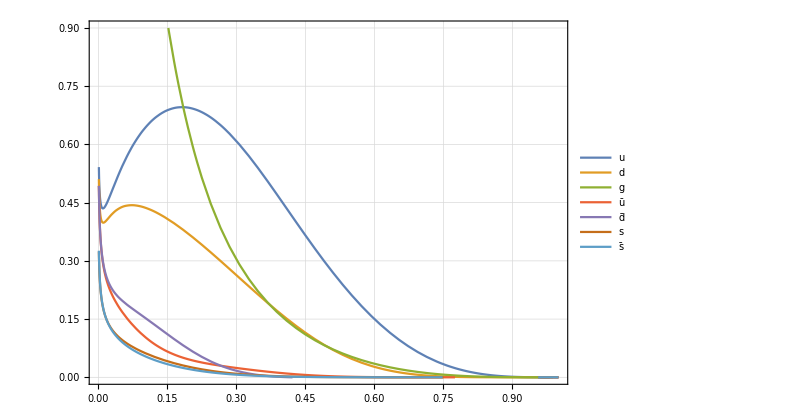

```mathematica
(* Plot PDF : Peskin pg 563 *)
uppdf=xf[0,x,2,2];
downpdf=xf[0,x,2,1];
gluepdf=xf[0,x,2,0];
upbarpdf=xf[0,x,2,-2];
dbarpdf=xf[0,x,2,-1];
spdf=xf[0,x,2,3];
sbarpdf=xf[0,x,2,-3];
Plot[{uppdf,downpdf,gluepdf,upbarpdf,dbarpdf,spdf,sbarpdf},{x,0.001,1},PlotRange->{{0,1},{0,0.9}},PlotLegends->{"u","d","g","ū","d̄","s","s̄"}]
```

```mathematica
Definitions;

ecoll=13000;
scoll=ecoll^2;

pdf[x_,Q_,flav_]:=If[x<1.0&&x>10^-7,1/x xf[0,x,Q,flav],0]

(* remember: quarkID = 2 (up), 1 (down),   gluon = 0 *)

(* Parton Luminosity (Factorization) *)
Lq[list_,ecoll_,M1_,M2_,quarkID_]:=Block[{ArrayL1,Mcounts,Mvalue,IntL,Qgluon},
ArrayL1={};
Mcounts=71;
If[quarkID==0,Qgluon=-1,Qgluon=1];
Monitor[For[j=1,j≤Mcounts,j+=1,
Mvalue=(M1+(M2-M1)/(Mcounts-1)(j-1))//N;
AppendTo[ArrayL1,{Mvalue,(2Mvalue)/ecoll^2 NIntegrate[1/(x((1-Qgluon)/2+1))(pdf[x, Mvalue,quarkID]pdf[Mvalue^2/(x ecoll^2), Mvalue,-quarkID]+pdf[x, Mvalue,-quarkID]pdf[Mvalue^2/(x ecoll^2), Mvalue,quarkID]),{x,Mvalue^2/ecoll^2,1}]}];
(*((1-Qgluon)/2+1) for glue-glue collision*) (* 2Mvalue comes from d/dM^2 -> 1/(2M)d/dM*)

],j];
(* Interpolate *)
IntL=Interpolation[ArrayL1];
(* Output *)
If[list==1,Return[ArrayL1],Return[IntL]]
]

(* We now calculate the DATA for the Luminosity functions to be used later *)

LupList=     Lq[1,ecoll,200,2700,2];
(*Export["~/Dropbox/1_Dilepton_study/Luminosity_up_list.txt",LupList];*)
LdownList=Lq[1,ecoll,200,2700,1];
(*Export["~/Dropbox/1_Dilepton_study/Luminosity_down_list.txt",LdownList];*)
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00198438}. NIntegrate obtained 20454.6 and 0.0538602 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00353391}. NIntegrate obtained 7884.36 and 0.0461802 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00364346}. NIntegrate obtained 5306.85 and 0.0542181 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00198438}. NIntegrate obtained 14012. and 0.047969 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00113718}. NIntegrate obtained 8284.32 and 0.11247 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.00124427}. NIntegrate obtained 5232.52 and 0.0163072 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

InterpolatingFunction[…]

InterpolatingFunction[…]

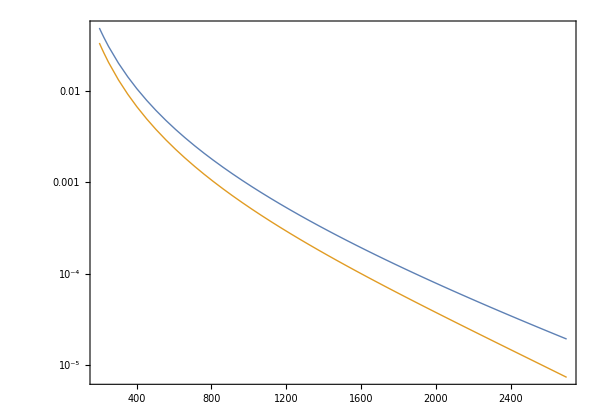

```mathematica
(* We now interpolate the data *)
Lup=     Interpolation[LupList]
Ldown=Interpolation[LdownList]

LogPlot[{Lup[x],Ldown[x]},{x,200,2700},Frame->True,PlotRange->All]
```

### Proton Level Calculation

#### dσ/dM Calculation

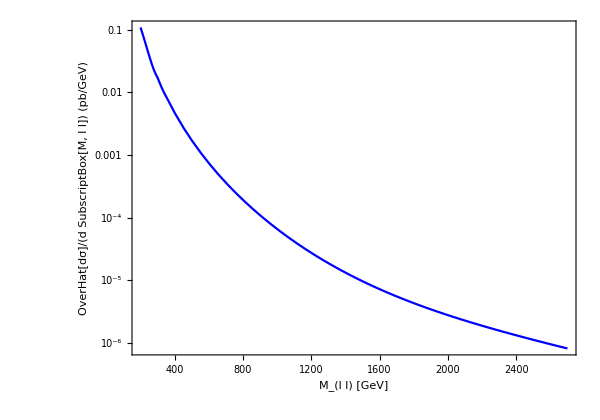

```mathematica
dσdCθdM[M_]:=Lup[M] (dσuu2lldCθwil/.{Ein->M/2})+Ldown[M] (dσdd2lldCθwil/.{Ein->M/2})

DataPoints=51;
InitialPoint=200;
FinalPoint=2700;
Step=(FinalPoint-InitialPoint)/(DataPoints-1)//N;

dσdM[M_]:=NIntegrate[dσdCθdM[M],{Cθ,-1,1}]

dσdMlist={};

Monitor[For[j=1,j≤DataPoints,j+=1,

MVal=InitialPoint+Step(j-1);

AppendTo[dσdMlist,{MVal,dσdM[MVal]}];

],j];

dσdMIn=Interpolation[dσdMlist];

dσdMplot=LogPlot[dσdMIn[M],{M,200,2700},PlotStyle->{Blue},PlotRange->All,FrameLabel->{"M_(l l) [GeV]",Style["OverHat[dσ]/(d SubscriptBox[M, l l]) (pb/GeV)"],"DiLepton - proton Level"}];
Show[dσdMplot]
```

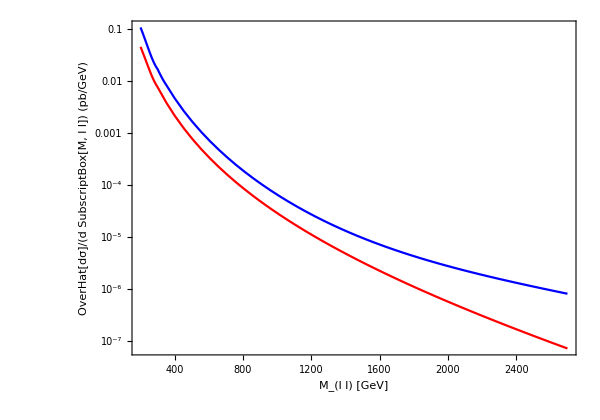

```mathematica
dσdCθdMSM[M_]:=Lup[M] (dσuu2lldCθSM/.{Ein->M/2})+Ldown[M] (dσdd2lldCθSM/.{Ein->M/2})

DataPoints=51;
InitialPoint=200;
FinalPoint=2700;
Step=(FinalPoint-InitialPoint)/(DataPoints-1)//N;

dσdMSM[M_]:=NIntegrate[dσdCθdMSM[M],{Cθ,-1,1}]

dσdMSMlist={};

Monitor[For[j=1,j≤DataPoints,j+=1,

MVal=InitialPoint+Step(j-1);

AppendTo[dσdMSMlist,{MVal,dσdMSM[MVal]}];

],j];

dσdMSMIn=Interpolation[dσdMSMlist];

dσdMSMplot=LogPlot[dσdMSMIn[M],{M,200,2700},PlotStyle->{Red},PlotRange->All,FrameLabel->{"M_(l l) [GeV]",Style["OverHat[dσ]/(d SubscriptBox[M, l l]) (pb/GeV)"],"DiLepton - proton Level"}];
Show[dσdMplot,dσdMSMplot]
```